```mathematica
PtxS = 10^-3;
```

```mathematica
PtxD = 0.5*10^-3;
```

```mathematica
PtxDC = 10^-2;
```

```mathematica
rSD = 50;
rDU = 50;
rSU = 50*Sqrt[2];
rDCU = 50;
rDCD= 50*Sqrt[2];
```

```mathematica
n = 10^-11; (*Thermal noise*)
pathloss = 4; (*Path loss exponent*)
vSU = 1;
hSU = PtxS/rSU^pathloss;
```

```mathematica
vDCU = 1;
hDCU = PtxDC/rDCU^pathloss;
```

```mathematica
vSD = 1;
hSD= PtxS/rSD^pathloss;
vDCD =1;
hDCD = PtxDC/rDCD^pathloss;
vDU = 1;
hDU = PtxD/rDU^pathloss;
```

```mathematica
PlinkStoU= N[Exp[-(pathloss *n)/(vSU *hSU)],3];
PlinkDtoU= N[Exp[-(pathloss *n)/(vDU *hDU)],3];
PlinkDCtoU =N[ Exp[-(pathloss*n)/(vDCU*hDCU)],3];
PlinkDCtoUwhenS = PlinkDCtoU/(1+pathloss*(vSU*hSU)/(vDCU*hDCU));
PlinkStoD = N[Exp[-(pathloss*n)/(vSD*hSD)],3];
PlinkStoDwhenD = PlinkStoD;
PlinkStoDwhenDC= PlinkStoD/(1+pathloss*(vDCD*hDCD)/(vSD*hSD));
PlinkDtoUwhenS= PlinkDtoU/(1+pathloss*(vSU*hSU)/(vDU*hDU));
```

```mathematica
δ=1/2;
numFiles = 10000;
Ω =N[1/(∑_(j=1)^numFiles j^-δ),3];
P[i_]:=Ω/i^δ;
∑_(i=1)^numFiles P[i];
Mu = 200
Md = 1000;
Ms = 2500;
qu= 1-∑_(i=1)^Mu P[i]
phd= ∑_(i=Mu+1)^Md P[i]
phs= ∑_(i=Md+1)^Ms P[i]
```

```mathematica
(*Table[qu[Muser], {Muser, 100, 1000, 100}]
Table[phd[Muser,Md], {Muser, 100, 1000, 100}]
phs*)
```

{0.9617[100],0.9617[200],0.9617[300],0.9617[400],0.9617[500],0.9617[600],0.9617[700],0.9617[800],0.9617[900],0.9617[1000]}

{0.273[100,1000],0.273[200,1000],0.273[300,1000],0.273[400,1000],0.273[500,1000],0.273[600,1000],0.273[700,1000],0.273[800,1000],0.273[900,1000],0.273[1000,1000]}

0.185

```mathematica
μ[qs_, qd_, a_] :=qs*((1-qu)*PlinkStoD+qu*qd*phd*PlinkStoDwhenD+qu*(1-qd*phd)*a*PlinkStoDwhenDC+qu*(1-qd*phd)*(1-a)*PlinkStoD)
```

```mathematica
pQNotZero[λ_,qs_,qd_,a_] := λ/μ[qs,qd,a]
pQZero[λ_,qs_,qd_, a_] := 1-pQNotZero[λ,qs,qd, a];
```

```mathematica
ThroughputUser[qs_, qd_, qc_, a_ , λ_] := pQZero[λ,qs,qd, a]*qu*(qd*PlinkDtoU + (1-qd*phd)*qc*phs*PlinkStoU+(1-qd*phd)*(1-qc*phs)*a*PlinkDCtoU)+\
			  +pQNotZero[λ,qs,qd, a]*qu*qs*(qd*phd*PlinkDtoUwhenS+(1-qd*phd)*a*PlinkDCtoUwhenS)+\
			    +pQNotZero[λ,qs,qd, a]*qu*(1-qs)*(qd*phd*PlinkDtoU+(1-qd*phd)*qc*phs*PlinkStoU+(1-qd*phd)*(1-qc*phs)*a*PlinkDCtoU)
```

```mathematica
mu[a_] := NMaximize[ {μ[qs, qd, a], 0≤qs≤1 && 0≤qd≤1 && 0≤a≤1},{qs, qd}]
```

```mathematica
T[λ_,w_]:=NMaximize[ {w*λ+ (1-w)*ThroughputUser[qs, qd, qc, 0.7, λ], \
		0<=λ<μ[qs, qd, 0.7] && 0≤qs≤1 && 0≤qd≤1&& 0≤qc≤1 }, {qs, qd, qc} ]
```

```mathematica
maxWeightedSum14=Table[ {N[lambda/100], T[lambda/100, 1/4][[1]] },{lambda, 2,68,2}]
```

NMaximize::nsol: There are no points that satisfy the constraints {11/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {23/50-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {12/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

General::stop: Further output of NMaximize::nsol will be suppressed during this calculation.

{{0.02,0.655168},{0.04,0.644379},{0.06,0.63359},{0.08,0.622801},{0.1,0.612012},{0.12,0.601222},{0.14,0.590433},{0.16,0.579644},{0.18,0.568855},{0.2,0.558066},{0.22,0.547277},{0.24,0.536487},{0.26,0.525698},{0.28,0.514909},{0.3,0.50412},{0.32,0.493331},{0.34,0.482541},{0.36,0.471752},{0.38,0.460963},{0.4,0.450174},{0.42,0.439385},{0.44,-∞},{0.46,-∞},{0.48,-∞},{0.5,-∞},{0.52,-∞},{0.54,-∞},{0.56,-∞},{0.58,-∞},{0.6,-∞},{0.62,-∞},{0.64,-∞},{0.66,-∞},{0.68,-∞}}

```mathematica
maxWeightedSum24=Table[ {N[lambda/100], T[lambda/100, 2/4][[1]] },{lambda, 2,68,2}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::nsol: There are no points that satisfy the constraints {11/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {23/50-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {12/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

General::stop: Further output of NMaximize::nsol will be suppressed during this calculation.

{{0.02,0.443446},{0.04,0.442919},{0.06,0.442393},{0.08,0.441867},{0.1,0.441341},{0.12,0.440815},{0.14,0.440289},{0.16,0.439763},{0.18,0.439237},{0.2,0.43871},{0.22,0.438184},{0.24,0.437658},{0.26,0.437132},{0.28,0.436606},{0.3,0.43608},{0.32,0.435554},{0.34,0.435028},{0.36,0.434501},{0.38,0.433975},{0.4,0.433449},{0.42,0.432923},{0.44,-∞},{0.46,-∞},{0.48,-∞},{0.5,-∞},{0.52,-∞},{0.54,-∞},{0.56,-∞},{0.58,-∞},{0.6,-∞},{0.62,-∞},{0.64,-∞},{0.66,-∞},{0.68,-∞}}

```mathematica
maxWeightedSum34=Table[ {N[lambda/100], T[lambda/100, 3/4][[1]] },{lambda, 2,68,2}]
```

NMaximize::nsol: There are no points that satisfy the constraints {11/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {23/50-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

NMaximize::nsol: There are no points that satisfy the constraints {12/25-0.437466 qs≤0,-qc≤0,-qd≤0,-qs≤0,-1+qc≤0,-1+qd≤0,-1+qs≤0}.

General::stop: Further output of NMaximize::nsol will be suppressed during this calculation.

{{0.02,0.231723},{0.04,0.24146},{0.06,0.251197},{0.08,0.260934},{0.1,0.270671},{0.12,0.280407},{0.14,0.290144},{0.16,0.299881},{0.18,0.309618},{0.2,0.319355},{0.22,0.329092},{0.24,0.338829},{0.26,0.348566},{0.28,0.358303},{0.3,0.36804},{0.32,0.377777},{0.34,0.387514},{0.36,0.397251},{0.38,0.406988},{0.4,0.416725},{0.42,0.426462},{0.44,-∞},{0.46,-∞},{0.48,-∞},{0.5,-∞},{0.52,-∞},{0.54,-∞},{0.56,-∞},{0.58,-∞},{0.6,-∞},{0.62,-∞},{0.64,-∞},{0.66,-∞},{0.68,-∞}}

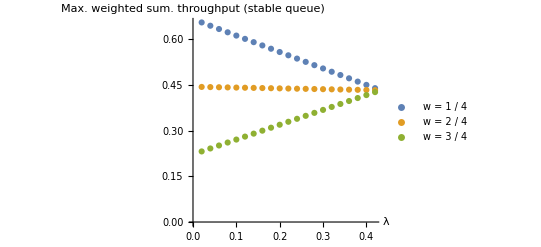

```mathematica
maxPlot = ListPlot[ {maxWeightedSum14, maxWeightedSum24, maxWeightedSum34}, AxesLabel->{ Style["λ", Italic,14], Style["Max. weighted sum. throughput (stable queue)", Italic, 12]}, AxesStyle->Thick,PlotLegends->{"w = 1 / 4","w = 2 / 4","w = 3 / 4"}]
```

```mathematica
(*Export2PDF[PlotName_]:=Module[{A=600},Export[SystemDialogInput["FileSave",StringJoin[{ToString[FileName],".eps"}]],PlotName,"AllowRasterization"->True,ImageSize->Full  ,ImageResolution->500]]*)
```